# Laboratorio 2 Mat1630L

## Preguntas

### 1)

a) Como la tercera componente es Cos(t), entonces al menor el intervalo tiene que tener largo 2π. Es fácil ver, graficando, que la curva se grafica completa en el intervalo [0,2π].

```mathematica
g[t_]:={Sin[t]+Cos[2*t],Cos[2t],Cos[t]}
ParametricPlot3D[g[t],{t,0,2Pi}]
```

-Graphics3D-

b)

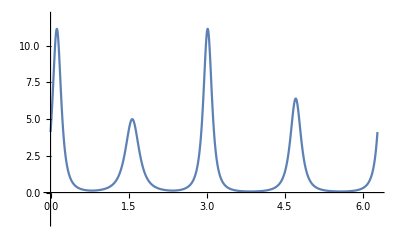

```mathematica
κ[t_]:=Norm[Cross[g'[t],g''[t]]]/(Norm[g'[t]])^3
Plot[κ[t],{t,0,2*Pi},PlotRange->{{0,2Pi},{-2,12}}]
```

c)

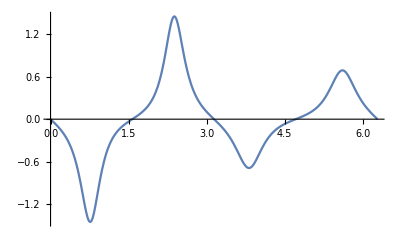

```mathematica
τ[t_]:=g'[t].Cross[g'''[t],g''[t]]/(Norm[Cross[g'[t],g''[t]]])^2
Plot[τ[t],{t,0,2*Pi}]
```

d)

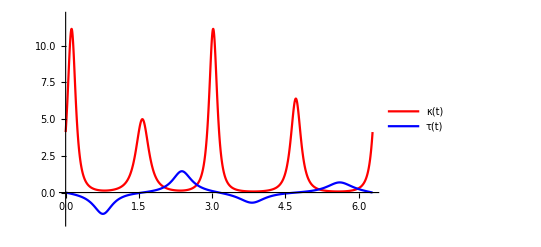

```mathematica
Plot[{κ[t],τ[t]},{t,0,2*Pi},PlotStyle->{Red,Blue},PlotRange->{{0,2Pi},{-2,12}},PlotLegends->"Expressions"]
```

e)
Vector tangente.

```mathematica
tangente[t_]=ComplexExpand[g'[t]/Norm[g'[t]]]
```

{Cos[t]/(√(Sin[t]^2+(Cos[t]-2 Sin[2 t])^2+4 Sin[2 t]^2))-(2 Sin[2 t])/(√(Sin[t]^2+(Cos[t]-2 Sin[2 t])^2+4 Sin[2 t]^2)),-(2 Sin[2 t])/(√(Sin[t]^2+(Cos[t]-2 Sin[2 t])^2+4 Sin[2 t]^2)),-Sin[t]/(√(Sin[t]^2+(Cos[t]-2 Sin[2 t])^2+4 Sin[2 t]^2))}

Vector normal.

```mathematica
normal[t_]=tangente'[t]/Norm[tangente'[t]]//Simplify
```

{(3-4 Cos[2 t]+Cos[4 t]-6 Sin[t]-6 Sin[3 t]-2 Sin[5 t])/(√(64 Abs[(Cos[2 t]-4 Cos[t]^4 Sin[t])/(5-4 Cos[4 t]-2 Sin[t]-2 Sin[3 t])^(3/2)]^2+Abs[(10 Cos[t]-12 Cos[3 t]+4 Cos[5 t]-6 Sin[2 t]+Sin[4 t])/(5-4 Cos[4 t]-2 Sin[t]-2 Sin[3 t])^(3/2)]^2+Abs[(3-4 Cos[2 t]+Cos[4 t]-6 Sin[t]-6 Sin[3 t]-2 Sin[5 t])/(5-4 Cos[4 t]-2 Sin[t]-2 Sin[3 t])^(3/2)]^2) (5-4 Cos[4 t]-2 Sin[t]-2 Sin[3 t])^(3/2)),-(8 (Cos[2 t]-4 Cos[t]^4 Sin[t]))/(√(64 Abs[(Cos[2 t]-4 Cos[t]^4 Sin[t])/(5-4 Cos[4 t]-2 Sin[t]-2 Sin[3 t])^(3/2)]^2+Abs[(10 Cos[t]-12 Cos[3 t]+4 Cos[5 t]-6 Sin[2 t]+Sin[4 t])/(5-4 Cos[4 t]-2 Sin[t]-2 Sin[3 t])^(3/2)]^2+Abs[(3-4 Cos[2 t]+Cos[4 t]-6 Sin[t]-6 Sin[3 t]-2 Sin[5 t])/(5-4 Cos[4 t]-2 Sin[t]-2 Sin[3 t])^(3/2)]^2) (5-4 Cos[4 t]-2 Sin[t]-2 Sin[3 t])^(3/2)),-(10 Cos[t]-12 Cos[3 t]+4 Cos[5 t]-6 Sin[2 t]+Sin[4 t])/(√(64 Abs[(Cos[2 t]-4 Cos[t]^4 Sin[t])/(5-4 Cos[4 t]-2 Sin[t]-2 Sin[3 t])^(3/2)]^2+Abs[(10 Cos[t]-12 Cos[3 t]+4 Cos[5 t]-6 Sin[2 t]+Sin[4 t])/(5-4 Cos[4 t]-2 Sin[t]-2 Sin[3 t])^(3/2)]^2+Abs[(3-4 Cos[2 t]+Cos[4 t]-6 Sin[t]-6 Sin[3 t]-2 Sin[5 t])/(5-4 Cos[4 t]-2 Sin[t]-2 Sin[3 t])^(3/2)]^2) (5-4 Cos[4 t]-2 Sin[t]-2 Sin[3 t])^(3/2))}

Vector binormal.

```mathematica
binormal[t_]=Cross[tangente[t],normal[t]]/Norm[Cross[tangente[t],normal[t]]]
```

{(-(8 Cos[2 t] Sin[t])/(√(64 Abs[(Cos[2 t]-1)/(1)^(3/2)]^2+Abs[1/1]^2+Abs[1/1^1]^2) √(Sin[t]^2+(1)^2+4 Sin[1]^2) (1)^(3/2))+(32 Cos[t]^4 Sin[t]^2)/(√1 √1 1)+6+(2 Sin[2 t] Sin[4 t])/(√(64 Abs[1/1]^2+Abs[1]^2+Abs[1]^2) √1 1))/(√(Abs[-(8 Cos[2 t] Sin[t])/1+(32 1^4 1^2)/1+6+(2 Sin[2 t] Sin[4 t])/(√(64 Abs[1]^2+1^2+1^2) √1 1)]^2+Abs[(10 1^2)/1-1/1+17+(2 Sin[t] Sin[5 t])/1]^2+Abs[1]^2)),1/(√1),(-(8 Cos[t] Cos[2 t])/(√1 √1 1)+12)/(√(Abs[1]^2+Abs[1]^2+Abs[1]^2))}
 |  |  |  |

Para mostrar que los vectores son perpendiculares entre si lo haremos ocupando el producto punto.

```mathematica
tangente[t].normal[t]//Simplify
tangente[t].binormal[t]//Simplify
normal[t].binormal[t]//Simplify
```

0

0

0

f)

```mathematica
Vector[inicio:{_,_,_},final:{_,_,_},color_]:=Graphics3D[{color,CapForm["Butt"],Arrowheads[Small],Arrow[Tube[{inicio,inicio+final}]]}];
tan=Vector[g[0],tangente[0],Red];
nor=Vector[g[0],normal[0],Blue];
bin=Vector[g[0],binormal[0],Green];
curva=ParametricPlot3D[g[t],{t,0,2Pi}];
Show[tan,curva,nor,bin]
```

-Graphics3D-

g)

```mathematica
Vector[inicio:{_,_,_},final:{_,_,_},color_]:=Graphics3D[{color,CapForm["Butt"],Arrowheads[Small],Arrow[Tube[{inicio,inicio+final}]]}];
Animate[tan=Vector[g[p],tangente[p],Red];
nor=Vector[g[p],normal[p],Blue];
bin=Vector[g[p],binormal[p],Green];
curva=ParametricPlot3D[g[t],{t,0,2Pi}];
Show[tan,curva,nor,bin],{p,0,2Pi}]
```